## HMM with continuous observations (Problem 12.4)

```mathematica
Clear["Global`*"];
```

```mathematica
prior=0.999937;p1=(prior*0.9+(1-prior)*0.1)/((prior*0.9+(1-prior)*0.1)+(prior*0.1+(1-prior)*0.9)); p0=1-p1; σ=1/(2 √2 InverseErfc[2*0.1]); {p0,p1,σ}
```

{0.10005,0.89995,0.390152}

```mathematica
eq=(p0 PDF[NormalDistribution[0,σ],y]-p1 PDF[NormalDistribution[1,σ],y])
```

-0.920226 ⅇ^(-3.28475 (-1+y)^2)+0.102305 ⅇ^(-3.28475 y^2)

```mathematica
FindRoot[eq==0,{y,0}]  (* value where filter output switches from 0 -> 1 *)
```

{y→0.165627}

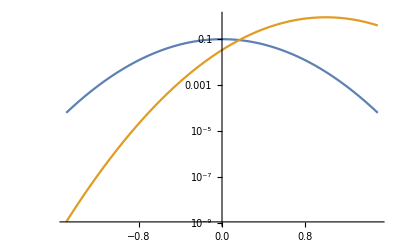

```mathematica
LogPlot[{p0 PDF[NormalDistribution[0,σ],y],p1 PDF[NormalDistribution[1,σ],y]},{y,-1.5,1.5}]
```

```mathematica
(p0 PDF[NormalDistribution[0,σ],y])/(p0 PDF[NormalDistribution[0,σ],y]+p1 PDF[NormalDistribution[1,σ],y])/.y->0.296013
```

0.298056